```mathematica
(* Import sequences *)

file="True IDR Domains without CRs.fasta";

Header=Import[file,"Header"];
Length[Header]
Seq=Import[file,"Sequence"];
Length[Seq]
```

101

101

Spacer lengths (in aa):

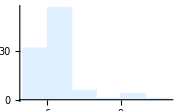

6.24837

0.921194

Motif density:

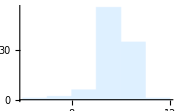

9.85201

0.756471

```mathematica
(* Hydro-Motif Spacing Analysis *)

AverageSpacerLength={};
AverageNumberOfHydroMotif={};

Do[{holen=Seq[[a]];
NamenHolen=Header[[a]];

s1=Flatten[StringSplit[holen,"FG"]];
s2=Flatten[StringSplit[s1,"LG"]];
s3=Flatten[StringSplit[s2,"MG"]];
s4=Flatten[StringSplit[s3,"IG"]];
s5=Flatten[StringSplit[s4,"WG"]];
s6=Flatten[StringSplit[s5,"GF"]];
s7=Flatten[StringSplit[s6,"YS"]];
s8=Flatten[StringSplit[s7,"FS"]];

Durschschnitt=(N[Mean[StringLength[s8]]]/StringLength[holen])*100;
AverageSpacerLength=AppendTo[AverageSpacerLength,Durschschnitt];
Abweichung=N[StandardDeviation[StringLength[s8]]];

AverageNumberOfHydroMotif=AppendTo[AverageNumberOfHydroMotif,(((Length[s8]-1)/StringLength[holen])*100)]

},{a,1,Length[Seq]}]

Print["Spacer lengths (in aa):"]
spacerPlot=Histogram[AverageSpacerLength,{1}, 
ChartStyle->LightBlue,
ImageSize->Small,
PlotRange->Full]
N[Mean[AverageSpacerLength]]
N[StandardDeviation[AverageSpacerLength]]

Print["Motif density:"]
motifPlot=Histogram[AverageNumberOfHydroMotif,{1},
ChartStyle->LightBlue,
ImageSize->Small,
PlotRange->Full]
N[Mean[AverageNumberOfHydroMotif]]
N[StandardDeviation[AverageNumberOfHydroMotif]]
```

```mathematica
(* Export the data *)

dir=DirectoryName[file];
SetDirectory[dir];
newdir=CreateDirectory["True IDR analysis/Motif analysis"];
SetDirectory[newdir];

Export["SpacerLength.pdf",spacerPlot]
Export["MotifNumber.pdf",motifPlot]
```

SpacerLength.pdf

MotifNumber.pdf